## Continuous One-Patch case

```mathematica
q1=0;
```

```mathematica
q2= (α (X-Y))/(2 δ+α(X+Y));
q3=(α (X-Y))/(δ+α Y);
q4= (α (X-Y))/(δ+α Y);
```

```mathematica
sub=Solve[{q2==b},{X}][[1]]//Simplify
```

{X→((1+b) Y α+2 b δ)/(α-b α)}

```mathematica
q3/.sub//Simplify
```

b

```mathematica
q4/.sub//Simplify
```

-(2 b)/(-1+b)

There is only one degree of freedom in this model.  Given that cycling rate doesn’t intuitively matter the stability of the boundary equilibrium could matter.

```mathematica
Solve[{q2==b,q3==c},{X,α}]
```

{}

```mathematica
sub/.Y-> 0.1/.α-> 1/.δ-> 0.5/.b-> {0.1,0.2,0.3}
```

{X→{0.233333,0.4,0.614286}}

```mathematica
q3/.sub/.Y-> 0.1/.α-> 1/.δ-> 0.5/.b-> {0.1,0.2,0.3}
```

{0.222222,0.5,0.857143}

## Continuous Two-Patch Case

```mathematica
q1=-(2(ϕ+ω))/(2 δ+ α(X+Y));
q2= (α (X-Y))/(2 δ+α(X+Y));
q3=(α (X-Y)- 2 ϕ)/(δ+α X);
q4= (α (X-Y)- 2 ω)/(δ+α Y);
```

```mathematica
sub=Solve[{q1==Subscript[λ, in],q2==Subscript[λ, ini],q3==Subscript[λ, mb]},{X,Y,ω}]//FullSimplify
```

{{X→-(δ+(2 ϕ (1+λ_ini))/(λ_ini (-2+λ_mb)+λ_mb))/α,Y→(-δ+(2 ϕ (-1+λ_ini))/(λ_ini (-2+λ_mb)+λ_mb))/α,ω→ϕ (-1+(2 λ_in)/(λ_ini (-2+λ_mb)+λ_mb))}}

```mathematica
q4/.sub//Simplify
```

{(-2 a+b (-4+c)+c)/(-1+b)}

There are three independent dimensions here: The stability of the internal equilibria, the cycling rate, and the instability of the boundary equilibria.

```mathematica
sub/.α-> 1/.δ-> 0.5/.ϕ-> 0.01
```

{{X→-(0.02+b (0.02+0.5 (-2+c))+0.5 c)/(b (-2+c)+c),Y→-((0.02+b (-0.02+0.5 (-2+c))+0.5 c)/(b (-2+c)+c)),ω→(0.01 (2 a-b (-2+c)-c))/(b (-2+c)+c)}}

```mathematica
Reduce[{1>-((0.02+b (0.02+0.5 (-2+c))+0.5 c)/(b (-2+c)+c))>0,1>-((0.02+b (-0.02+0.5 (-2+c))+0.5 c)/(b (-2+c)+c))>0,1>(0.01 (2 a-b (-2+c)-c))/(b (-2+c)+c)>0,c==0.16}]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

((-1.80511<a≤-0.737226&&0.000430478 (202.-25. a)<b<0.106383)||(-0.737226<a≤-0.0178723&&0.0948905<b<0.106383)||(-0.0178723<a<-0.00729927&&0.0948905<b<0.0434783 (2.-25. a)))&&c==0.16

```mathematica
{{a, b, c, i}, {-0.1, 0.095, 0.15, 18}, {-0.1, 0.0975, 0.15, 19}, {-0.1, 0.1, 0.15, 20}, {-0.1, 0.095, 0.155, 21}, {-0.1, 0.0975, 0.155, 22}, {-0.1, 0.1, 0.155, 23}, {-0.1, 0.095, 0.16, 24}, {-0.1, 0.0975, 0.16, 25}, {-0.1, 0.1, 0.16, 26}, {-0.3, 0.095, 0.15, 27}, {-0.3, 0.0975, 0.15, 28}, {-0.3, 0.1, 0.15, 29}, {-0.3, 0.095, 0.155, 30}, {-0.3, 0.0975, 0.155, 31}, {-0.3, 0.1, 0.155, 32}, {-0.3, 0.095, 0.16, 33}, {-0.3, 0.0975, 0.16, 34}, {-0.3, 0.1, 0.16, 35}, {-0.5, 0.095, 0.15, 36}, {-0.5, 0.0975, 0.15, 37}, {-0.5, 0.1, 0.15, 38}, {-0.5, 0.095, 0.155, 39}, {-0.5, 0.0975, 0.155, 40}, {-0.5, 0.1, 0.155, 41}, {-0.5, 0.095, 0.16, 42}, {-0.5, 0.0975, 0.16, 43}, {-0.5, 0.1, 0.16, 44}}
```

```mathematica
sub/.α-> 1/.δ-> 0.5/.ϕ-> 0.01/.a-> -0.5/.b-> 0.095/.c-> 0.16
sub/.α-> 1/.δ-> 0.5/.ϕ-> 0.01/.a-> -0.5/.b-> 0.0975/.c-> 0.16
sub/.α-> 1/.δ-> 0.5/.ϕ-> 0.01/.a-> -0.5/.b-> 0.1/.c-> 0.16
```

{{X→0.97973,Y→0.722973,ω→0.665676}}

{{X→0.631443,Y→0.430412,ω→0.505464}}

{{X→0.416667,Y→0.25,ω→0.406667}}

## Continuous Island-Mainland Case

```mathematica
q1=-(ϕ+ω)/(2 δ+ α(X+Y));
q2= (α (X-Y))/(2 δ+α(X+Y));
q3=(α (X-Y))/(δ+α X);
q4= (α (X-Y))/(δ+α Y);
```

We can choose the magnitude of the real part of the internal equilibrium and the imaginary part of the equilibrium

```mathematica
sub=Solve[{q1==a,q2==b},{X,Y}][[1]]//Simplify
```

{X→-(2 a δ+(1+b) (ϕ+ω))/(2 a α),Y→(-2 a δ+(-1+b) (ϕ+ω))/(2 a α)}

But given these two things, the stability of the boundary equilibria are fixed.

```mathematica
q3/.sub//Simplify
```

(2 b)/(1+b)

```mathematica
q4/.sub//Simplify
```

-(2 b)/(-1+b)

These means we can’t separate out impacts of these three quantities on the dynamics and hence on genetic variation.  We can however show the relative impacts of the quantity a (which determines the stability) and b (which determines both the frequency of cycles and the instability of the boundary).  So what I would recommend doing is choosing a range of values for both a and b and make a facet plot showing if and how the maintenance of variation depends on these two quantities.

```mathematica
sub/.α-> 1/.δ-> 0.5/.ϕ-> 0.05/.ω-> 0.05
```

{X→(1. b+(1+b) Y)/(1-b),0.05→(0.05-0.05 b+2 a (0.5+Y))/(-1+b)}

```mathematica
Reduce[{1>-(1. a+0.1 (1+b))/(2 a)>0,1>(-1. a+0.1 (-1+b))/(2 a)>0}]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

(-0.5<b≤0&&0.1 (-1.-1. b)<a<0.0333333 (-1.+b))||(0<b<0.5&&0.1 (-1.+b)<a<0.0333333 (-1.-1. b))

```mathematica
a->0.1 (-1.+b)+0.01/.b-> 0.2
a->0.1 (-1.+b)+0.02/.b-> 0.2
a->0.1 (-1.+b)+0.03/.b-> 0.2
```

a→-0.07

a→-0.06

a→-0.05

```mathematica
Table[(sub/.α-> 1/.δ-> 0.5/.ϕ-> 0.05/.ω-> 0.05/.a->-0.07/.b->0.25)[[i,2]],{i,1,2}]
```

{0.392857,0.0357143}

```mathematica
Table[1/300*(sub/.α-> 1/.δ-> 0.5/.ϕ-> 0.05/.ω-> 0.05/.a->-0.07/.b->0.2)[[i,2]],{i,1,2}]
Table[1/300*(sub/.α-> 1/.δ-> 0.5/.ϕ-> 0.05/.ω-> 0.05/.a->-0.06/.b->0.2)[[i,2]],{i,1,2}]
Table[1/300*(sub/.α-> 1/.δ-> 0.5/.ϕ-> 0.05/.ω-> 0.05/.a->-0.05/.b->0.2)[[i,2]],{i,1,2}]
Table[1/300*(sub/.α-> 1/.δ-> 0.5/.ϕ-> 0.05/.ω-> 0.05/.a->-0.07/.b->0.225)[[i,2]],{i,1,2}]
Table[1/300*(sub/.α-> 1/.δ-> 0.5/.ϕ-> 0.05/.ω-> 0.05/.a->-0.06/.b->0.225)[[i,2]],{i,1,2}]
Table[1/300*(sub/.α-> 1/.δ-> 0.5/.ϕ-> 0.05/.ω-> 0.05/.a->-0.05/.b->0.225)[[i,2]],{i,1,2}]
Table[1/300*(sub/.α-> 1/.δ-> 0.5/.ϕ-> 0.05/.ω-> 0.05/.a->-0.07/.b->0.25)[[i,2]],{i,1,2}]
Table[1/300*(sub/.α-> 1/.δ-> 0.5/.ϕ-> 0.05/.ω-> 0.05/.a->-0.06/.b->0.25)[[i,2]],{i,1,2}]
Table[1/300*(sub/.α-> 1/.δ-> 0.5/.ϕ-> 0.05/.ω-> 0.05/.a->-0.05/.b->0.25)[[i,2]],{i,1,2}]
```

{0.00119048,0.000238095}

{0.00166667,0.000555556}

{0.00233333,0.001}

{0.00125,0.000178571}

{0.00173611,0.000486111}

{0.00241667,0.000916667}

{0.00130952,0.000119048}

{0.00180556,0.000416667}

{0.0025,0.000833333}

## Discrete One-Patch

```mathematica
q2=(S √((S-2)V((S-2)V-2)))/((S-2)((S-2)V-2));(*Internal cycling and internal instability*)
q3=(1-V(1-S))/(1-V);(*Matching boundary*)
q4=1/(1-S);(*Non-matching boundary*)
```

```mathematica
sub=Solve[{q2==a, q4==b},{S,V}][[1]]//Simplify
```

{S→(-1+b)/b,V→-(2 a^2 b (1+b))/(-(-1+b)^2+a^2 (1+b)^2)}

```mathematica
q2/.sub//FullSimplify
```

(√((a^2 (-1+b^2)^2)/(((-1+b)^2-a^2 (1+b)^2)^2)) ((-1+b)^2-a^2 (1+b)^2))/(-1+b^2)

```mathematica
q4/.sub/.a-> 0.2/.b-> 1.1
```

26.159

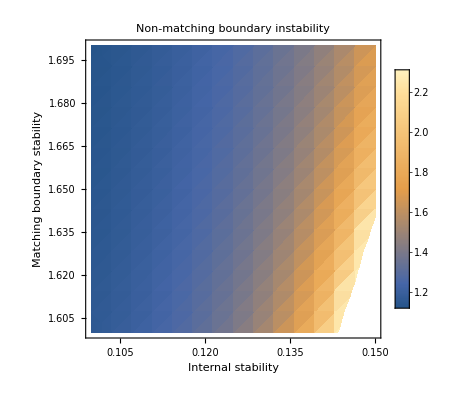

```mathematica
DensityPlot[q3/.sub,{a,0.1,0.15},{b,1.6,1.7},PlotLegends->Automatic,Frame-> True,FrameLabel-> {"Internal stability","Matching boundary stability"},PlotLabel-> "Non-matching boundary instability"]
```

```mathematica
Reduce[{1>(-1+b)/b>0,1>-(2 a^2 b (1+b))/(-(-1+b)^2+a^2 (1+b)^2)>0,a==0.15}]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

b>1.57626&&a==0.15

```mathematica
Table[(sub/.a->0.1/.b->1.6)[[i,2]],{i,1,2}]
Table[(sub/.a->0.1/.b->1.65)[[i,2]],{i,1,2}]
Table[(sub/.a->0.1/.b->1.7)[[i,2]],{i,1,2}]
Table[(sub/.a->0.125/.b->1.6)[[i,2]],{i,1,2}]
Table[(sub/.a->0.125/.b->1.65)[[i,2]],{i,1,2}]
Table[(sub/.a->0.125/.b->1.7)[[i,2]],{i,1,2}]
Table[(sub/.a->0.15/.b->1.6)[[i,2]],{i,1,2}]
Table[(sub/.a->0.15/.b->1.65)[[i,2]],{i,1,2}]
Table[(sub/.a->0.15/.b->1.7)[[i,2]],{i,1,2}]
```

{0.375,0.284542}

{0.393939,0.248244}

{0.411765,0.220091}

{0.375,0.511057}

{0.393939,0.436868}

{0.411765,0.381388}

{0.375,0.900433}

{0.393939,0.743921}

{0.411765,0.633638}

```mathematica
Table[(sub/.a->0.1/.b->1.7)[[i,2]],{i,1,2}]
Table[(sub/.a->0.125/.b->1.65)[[i,2]],{i,1,2}]
Table[(sub/.a->0.15/.b->1.6)[[i,2]],{i,1,2}]
```

{0.411765,0.220091}

{0.393939,0.436868}

{0.375,0.900433}

### Individual-Based Simulations

```mathematica
alist={0.1,0.1,0.1,0.125,0.125,0.125,0.15,0.15,0.15};
blist={1.6,1.65,1.7,1.6,1.65,1.7,1.6,1.65,1.7};
```

Absolute fitness values

```mathematica
WH[1,pVec_]:=pVec[[2]](1-V) +(1-pVec[[2]])S +(1-pVec[[2]])(1-S)(1-V);
WH[2,pVec_]:=(1-pVec[[2]])(1-V)+pVec[[2]]S +pVec[[2]](1-S)(1-V)  ;
WP[1,pVec_]:=pVec[[1]]+(1-pVec[[1]])(1-S);
WP[2,pVec_]:=(1-pVec[[1]])+pVec[[1]](1-S);
```

```mathematica
WH[2,{0.5,0.5}]/.S-> 0
```

0.+1. (1-V)

Relative fitness values

```mathematica
wH[pVec_]:=WH[1,pVec]/(pVec[[1]] WH[1,pVec]+(1-pVec[[1]])WH[2,pVec]) ;
wP[pVec_]:=WP[1,pVec]/(pVec[[2]] WP[1,pVec]+(1-pVec[[2]])WP[2,pVec]) ;
```

```mathematica
Clear[Sim]
Sim[pars_,intS_]:=Sim[pars,intS]=Block[{out,g,nHs,nPs,nHprime,nPprime},out={{1/2,1/2}}//N;
For[g=1,g≤(tMax/.pars),g++,

(*Selection*)
nHs=RandomVariate[BinomialDistribution[(κH/.pars),Min[Max[wH[out[[-1]]]out[[-1,1]]/.pars,0],1]]];
nPs=RandomVariate[BinomialDistribution[(κP/.pars),Min[Max[wP[out[[-1]]]out[[-1,2]]/.pars,0],1]]];

(*Number of type 1 hosts and parasites in next generation*)
nHprime=RandomVariate[BinomialDistribution[κH/.pars,Min[Max[nHs/(κH/.pars)//N,0],1]]];
nPprime=RandomVariate[BinomialDistribution[κP/.pars,Min[Max[nPs/(κP/.pars)//N,0],1]]];
AppendTo[out,{nHprime/κH,nPprime/κP}/.pars//N]
];
out
]
```

```mathematica
Clear[parIter]
parIter[p_,intS_]:=parIter[p,intS]=Block[{SChoice,VChoice,aChoice,bChoice,parsN,parsC,HC,HN},

aChoice=alist[[p]];
bChoice=blist[[p]];
SChoice=Table[(sub/.a->aChoice/.b->bChoice)[[i,2]],{i,1,2}][[1]];
VChoice=Table[(sub/.a->aChoice/.b->bChoice)[[i,2]],{i,1,2}][[2]];

parsN={S-> 0,V->VChoice,κH->300,κP->300,tMax->175};
parsC={S-> SChoice,V->VChoice,κH->300,κP->300,tMax->175};

For[r=1,r≤intS,r++,
Sim[parsC,r];
Sim[parsN,r];
];

HN=Mean[Table[2 Sim[parsN,r][[125,1]](1-Sim[parsN,r][[125,1]]),{r,1,intS}]];
HC=Mean[Table[2 Sim[parsC,r][[125,1]](1-Sim[parsC,r][[125,1]]),{r,1,intS}]];

HC-HN

];
```

```mathematica
parIter[1,2000]
parIter[2,2000]
parIter[3,2000]
parIter[4,2000]
parIter[5,2000]
parIter[6,2000]
parIter[7,2000]
parIter[8,2000]
parIter[9,2000]
```

-0.114302

-0.111278

-0.108821

-0.163369

-0.156595

-0.143837

-0.215259

-0.217714

-0.210231

```mathematica
p=8;
aChoice=alist[[p]];
bChoice=blist[[p]];
SChoice=Table[(sub/.a->aChoice/.b->bChoice)[[i,2]],{i,1,2}][[1]];
VChoice=Table[(sub/.a->aChoice/.b->bChoice)[[i,2]],{i,1,2}][[2]];

parsN={S-> 0,V->0.5,κH->300,κP->300,tMax->175};
parsC={S-> SChoice,V->VChoice,κH->300,κP->300,tMax->175}
```

{S→0.393939,V→0.743921,κH→300,κP→300,tMax→175}

```mathematica
parsN1={S->0,V->0.2200911052505395,κH->300,κP->300,tMax->125};
parsN2={S->0,V->0.4368677407268642,κH->300,κP->300,tMax->125};
parsN3={S->0,V->0.7439211701599757,κH->300,κP->300,tMax->125};
pars1={S->0.4117647058823529,V->0.2200911052505395,κH->300,κP->300,tMax->125};
pars2={S->0.3939393939393939,V->0.4368677407268642,κH->300,κP->300,tMax->125};
pars3={S->0.3939393939393939,V->0.7439211701599757,κH->300,κP->300,tMax->125};
```

```mathematica
mean[parsN3]
```

{0.5,0.496741,0.493528,0.490051,0.487304,0.484905,0.481155,0.477722,0.47536,0.471793,0.468174,0.464921,0.462271,0.45931,0.456029,0.453785,0.451301,0.449529,0.447399,0.44357,0.442825,0.43947,0.435386,0.432203,0.428531,0.425416,0.422151,0.420175,0.416533,0.414673,0.412435,0.410521,0.406949,0.404338,0.401184,0.398836,0.397047,0.395405,0.39319,0.389977,0.387888,0.384878,0.381931,0.379816,0.378114,0.374589,0.37243,0.372343,0.369533,0.36681,0.365266,0.364414,0.363277,0.360439,0.358553,0.356035,0.353522,0.351162,0.347725,0.345828,0.343375,0.342136,0.340314,0.337516,0.335222,0.333526,0.331588,0.329134,0.326347,0.323569,0.320768,0.319061,0.316524,0.314596,0.313195,0.311414,0.309199,0.305537,0.30352,0.30248,0.299972,0.297797,0.296392,0.295941,0.292146,0.289853,0.28827,0.286598,0.285199,0.284119,0.282518,0.281542,0.2793,0.276513,0.274122,0.27094,0.267474,0.267327,0.265204,0.263629,0.26187,0.258988,0.25824,0.25685,0.254276,0.251847,0.250338,0.247968,0.245291,0.244296,0.242258,0.241347,0.239749,0.238489,0.235865,0.23403,0.230734,0.228344,0.227585,0.225048,0.223557,0.221562,0.222555,0.221597,0.219117,0.216981,0.216314,0.216251,0.213033,0.211623,0.210312,0.208406,0.206682,0.204549,0.203493,0.201443,0.200763,0.198954,0.198061,0.196305,0.194038,0.1927,0.191742,0.189478,0.189273,0.189422,0.189322,0.187802,0.185891,0.185525,0.184693,0.183036,0.182583,0.182246,0.180876,0.179707,0.177625,0.177617,0.176206,0.174897,0.173241,0.172201,0.171174,0.169644,0.168736,0.167477,0.166193,0.165096,0.164114,0.163221,0.162426,0.161016,0.158509,0.158394,0.15801,0.156622}

```mathematica
Clear[mean]
mean[pars_]:=mean[pars]=Mean[Table[2 Sim[pars,j][[;;,1]](1-Sim[pars,j][[;;,1]]),{j,1,2000}]]
```

```mathematica
Clear[SD]
SD[pars_]:=SD[pars]=Mean[Table[(2 Sim[pars,j][[;;,1]](1-Sim[pars,j][[;;,1]])-mean[pars])^2,{j,1,2000}]]//Sqrt;
```

```mathematica
leg=LineLegend[{Directive[Black],
Directive[Black,Dashed],
Directive[Red],
Directive[Blue],
Directive[Orange]},
{"Coevolutionary","Neutral",
 "i(λ_in) = 0.1, λ_nm = 1.7",
 "i(λ_in) = 0.125, λ_nm = 1.65",
 "i(λ_in) = 0.15, λ_nm = 1.6"}];
```

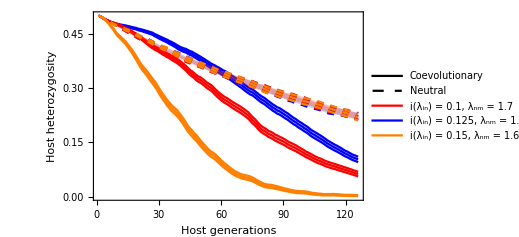

```mathematica
g=Show[ListLinePlot[{mean[parsN1],mean[parsN1]+(2SD[parsN1])/Sqrt[2000],mean[parsN1]-(2SD[parsN1])/Sqrt[2000]},PlotStyle->Directive[Blue,Dashed],Filling->{2->{{3},{Directive[Blue,Opacity[0.2]]}}}],ListLinePlot[{mean[pars1],mean[pars1]+(2SD[pars1])/Sqrt[2000],mean[pars1]-(2SD[pars1])/Sqrt[2000]},PlotStyle->Directive[Blue],Filling->{2->{{3},{Directive[Blue,Opacity[0.2]]}}}],
ListLinePlot[{mean[parsN2],mean[parsN2]+(2SD[parsN2])/Sqrt[2000],mean[parsN2]-(2SD[parsN2])/Sqrt[2000]},PlotStyle->Directive[Red,Dashed],Filling->{2->{{3},{Directive[Red,Opacity[0.2]]}}}],ListLinePlot[{mean[pars2],mean[pars2]+(2SD[pars2])/Sqrt[2000],mean[pars2]-(2SD[pars2])/Sqrt[2000]},PlotStyle->Directive[Red],Filling->{2->{{3},{Directive[Red,Opacity[0.2]]}}}],
ListLinePlot[{mean[parsN3],mean[parsN3]+(2SD[parsN3])/Sqrt[2000],mean[parsN3]-(2SD[parsN3])/Sqrt[2000]},PlotStyle->Directive[Orange,Dashed],Filling->{2->{{3},{Directive[Orange,Opacity[0.2]]}}}],
ListLinePlot[{mean[pars3],mean[pars3]+(2SD[pars3])/Sqrt[2000],mean[pars3]-(2SD[pars3])/Sqrt[2000]},PlotStyle->Directive[Orange],Filling->{2->{{3},{Directive[Orange,Opacity[0.2]]}}}],
PlotRange-> {0,0.5},Frame->True,FrameLabel-> {"Host generations","Host heterozygosity"},Axes-> False,Epilog->Inset[leg,Scaled[{0.25,0.25}]]]
```

```mathematica
Export["/Users/madeline/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/OnePatch_Discrete_Series.png",g,"PNG",ImageResolution-> 300]
```

/Users/madeline/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/OnePatch_Discrete_Series.png

```mathematica
Export["/Users/madeline/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/OnePatch_Discrete_DegreeFreedomSeries.png",%322,"PNG",ImageResolution-> 300]
```

/Users/madeline/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/OnePatch_Discrete_DegreeFreedomSeries.png

## Discrete Two-Patch

```mathematica
q2=(S √((S-2)V((S-2)V-2)))/((S-2)((S-2)V-2));(*Internal cycling*)
q3=(1-V(1-S))/(1-V);(*Matching boundary*)
q4=1/(1-S);(*Non-matching boundary*)
```

```mathematica
sub=Solve[{q2==a, q4==b},{S,V}][[1]]//Simplify
```

{S→(-1+b)/b,V→-(2 a^2 b (1+b))/(-(-1+b)^2+a^2 (1+b)^2)}

```mathematica
q2/.sub//FullSimplify
```

(√((a^2 (-1+b^2)^2)/(((-1+b)^2-a^2 (1+b)^2)^2)) ((-1+b)^2-a^2 (1+b)^2))/(-1+b^2)

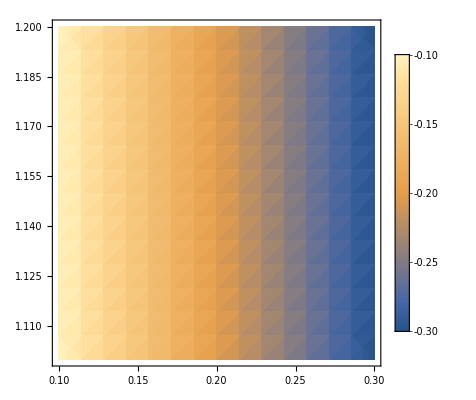

```mathematica
DensityPlot[q2/.sub,{a,0.1,0.3},{b,1.1,1.2},PlotLegends-> Automatic]
```

```mathematica
Reduce[{1>(-1+b)/b>0,1>-(2 a^2 b (1+b))/(-(-1+b)^2+a^2 (1+b)^2)>0,a==0.234}]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

b>1.8717&&a==0.2

```mathematica
Table[(sub/.a->0.1/.b->1.6)[[i,2]],{i,1,2}]
Table[(sub/.a->0.1/.b->1.65)[[i,2]],{i,1,2}]
Table[(sub/.a->0.1/.b->1.7)[[i,2]],{i,1,2}]
Table[(sub/.a->0.125/.b->1.6)[[i,2]],{i,1,2}]
Table[(sub/.a->0.125/.b->1.65)[[i,2]],{i,1,2}]
Table[(sub/.a->0.125/.b->1.7)[[i,2]],{i,1,2}]
Table[(sub/.a->0.15/.b->1.6)[[i,2]],{i,1,2}]
Table[(sub/.a->0.15/.b->1.65)[[i,2]],{i,1,2}]
Table[(sub/.a->0.15/.b->1.7)[[i,2]],{i,1,2}]
```

{0.375,0.284542}

{0.393939,0.248244}

{0.411765,0.220091}

{0.375,0.511057}

{0.393939,0.436868}

{0.411765,0.381388}

{0.375,0.900433}

{0.393939,0.743921}

{0.411765,0.633638}

### Individual-Based Simulations

```mathematica
alist={0.1,0.1,0.1,0.125,0.125,0.125,0.15,0.15,0.15};
blist={1.6,1.65,1.7,1.6,1.65,1.7,1.6,1.65,1.7};
```

Absolute fitness values

```mathematica
WH[1,u_,pVec_]:=pVec[[4-Mod[u,2]]](1-V) +(1-pVec[[4-Mod[u,2]]])S +(1-pVec[[4-Mod[u,2]]])(1-S)(1-V);
WH[2,u_,pVec_]:=(1-pVec[[4-Mod[u,2]]])(1-V)+pVec[[4-Mod[u,2]]]S +pVec[[4-Mod[u,2]]](1-S)(1-V)  ;
WP[1,u_,pVec_]:=pVec[[u]]+(1-pVec[[u]])(1-S);
WP[2,u_,pVec_]:=(1-pVec[[u]])+pVec[[u]](1-S);
```

Relative fitness values

```mathematica
wH[u_,pVec_]:=WH[1,u,pVec]/(pVec[[u]] WH[1,u,pVec]+(1-pVec[[u]])WH[2,u,pVec]) ;
wP[u_,pVec_]:=WP[1,u,pVec]/(pVec[[4-Mod[u,2]]] WP[1,u,pVec]+(1-pVec[[4-Mod[u,2]]])WP[2,u,pVec]) ;
```

```mathematica
Clear[Sim]
Sim[pars_,intS_]:=Sim[pars,intS]=Block[{out,g,nH1s,nP1s,nH2s,nP2s,nMH1,nMH2,nMP1,nMP2,nMH11,nMH12,nMH21,nMH22,nMP11,nMP12,nMP21,nMP22,nH1sm,nH2sm,nP1sm,nP2sm,nH11sm,nH21sm,nH12sm,nH22sm,nP11sm,nP12sm,nP21sm,nP22sm,nH1prime,nH2prime,nP1prime,nP2prime},out={{1/2,1/2,1/2,1/2}}//N;
For[g=1,g≤(tMax/.pars),g++,

(*Selection*)
nH1s=RandomVariate[BinomialDistribution[(κH/.pars),wH[1,out[[-1]]]out[[-1,1]]/.pars]];
nP1s=RandomVariate[BinomialDistribution[(κP/.pars),wP[1,out[[-1]]]out[[-1,3]]/.pars]];
nH2s=RandomVariate[BinomialDistribution[(κH/.pars),wH[2,out[[-1]]]out[[-1,2]]/.pars]];
nP2s=RandomVariate[BinomialDistribution[(κP/.pars),wP[2,out[[-1]]]out[[-1,4]]/.pars]];

(*Number of type 1 host migrants out of population 1*)
nMH11=RandomVariate[BinomialDistribution[nH1s,mH/.pars]];
nMH21=RandomVariate[BinomialDistribution[nH2s,mH/.pars]];

(*Number of type 2 host migrants out of population 1*)
nMH12=RandomVariate[BinomialDistribution[κH-nH1s/.pars,mH/.pars]];
nMH22=RandomVariate[BinomialDistribution[κH-nH2s/.pars,mH/.pars]];

(*Number of type 1 hosts after migration*)
nH11sm=nH1s-nMH11+nMH21;
nH21sm=nH2s-nMH21+nMH11;
 
(*Number of type 2 hosts after migration*)
nH12sm=κH-nH1s-nMH12+nMH22/.pars;
nH22sm=κH-nH2s-nMH22+nMH12/.pars;

(*Number of type 1 parasite migrants out of population 1*)
nMP11=RandomVariate[BinomialDistribution[nP1s,mP/.pars]];
nMP21=RandomVariate[BinomialDistribution[nP2s,mP/.pars]];

(*Number of type 2 parasite migrants out of population 1*)
nMP12=RandomVariate[BinomialDistribution[κP-nP1s/.pars,mP/.pars]];
nMP22=RandomVariate[BinomialDistribution[κP-nP2s/.pars,mP/.pars]];

(*Number of type 1 parasites after migration*)
nP11sm=nP1s-nMP11+nMP21;
nP21sm=nP2s-nMP21+nMP11;
 
(*Number of type 2 hosts after migration*)
nP12sm=κP-nP1s-nMP12+nMP22/.pars;
nP22sm=κP-nP2s-nMP22+nMP12/.pars;

AppendTo[out,{nH11sm/(nH11sm+nH12sm),nH21sm/(nH21sm+nH22sm),nP11sm/(nP11sm+nP12sm),nP21sm/(nP21sm+nP22sm)}/.pars//N]
];
out
]
```

```mathematica
Clear[parIter]
parIter[p_,intS_]:=parIter[p,intS]=Block[{SChoice,VChoice,aChoice,bChoice,parsN,parsC,HC,HN},

aChoice=alist[[p]];
bChoice=blist[[p]];
SChoice=Table[(sub/.a->aChoice/.b->bChoice)[[i,2]],{i,1,2}][[1]];
VChoice=Table[(sub/.a->aChoice/.b->bChoice)[[i,2]],{i,1,2}][[2]];

parsN={S-> 0,V->VChoice,mH->0.01,mP->0.01,κH->150,κP->150,tMax->125};
parsC={S-> SChoice,V->VChoice,mH->0.01,mP->0.01,κH->150,κP->150,tMax->125};

For[r=1,r≤intS,r++,
Sim[parsC,r];
Sim[parsN,r];
];

HN=Mean[Table[2 (1/2(Sim[parsN,j][[tMax/.parsN,1]]+Sim[parsN,j][[tMax/.parsN,2]]))(1-1/2(Sim[parsN,j][[tMax/.parsN,1]]+Sim[parsN,j][[tMax/.parsN,2]])),{j,1,intS}]];
HC=Mean[Table[2 (1/2(Sim[parsC,j][[tMax/.parsC,1]]+Sim[parsC,j][[tMax/.parsC,2]]))(1-1/2(Sim[parsC,j][[tMax/.parsC,1]]+Sim[parsC,j][[tMax/.parsC,2]])),{j,1,intS}]];

HC-HN

];
```

```mathematica
parIter[3,2000]
parIter[5,2000]
parIter[7,2000]
```

-0.0306889

-0.0647467

-0.295365

```mathematica
p=7;
aChoice=alist[[p]];
bChoice=blist[[p]];
SChoice=Table[(sub/.a->aChoice/.b->bChoice)[[i,2]],{i,1,2}][[1]];
VChoice=Table[(sub/.a->aChoice/.b->bChoice)[[i,2]],{i,1,2}][[2]];

parsN={S-> 0.5,V->VChoice,mH-> 0.01,mP-> 0.01,κH->150,κP->150,tMax->125}
parsC={S-> SChoice,V->VChoice,mH-> 0.01,mP-> 0.01,κH->150,κP->150,tMax->125}
```

{S→0.5,V→0.900433,mH→0.01,mP→0.01,κH→150,κP→150,tMax→125}

{S→0.375,V→0.900433,mH→0.01,mP→0.01,κH→150,κP→150,tMax→125}

```mathematica
parsN1={S->0,V->0.2200911052505395,mH->0.01,mP->0.01,κH->150,κP->150,tMax->125};
parsN2={S->0,V->0.4368677407268642,mH->0.01,mP->0.01,κH->150,κP->150,tMax->125};
parsN3={S->0,V->0.9004329004329,mH->0.01,mP->0.01,κH->150,κP->150,tMax->125};
pars1={S->0.4117647058823529,V->0.2200911052505395,mH->0.01,mP->0.01,κH->150,κP->150,tMax->125};
pars2={S->0.3939393939393939,V->0.4368677407268642,mH->0.01,mP->0.01,κH->150,κP->150,tMax->125};
pars3={S->0.37500000000000006,V->0.9004329004329,mH->0.01,mP->0.01,κH->150,κP->150,tMax->125};
```

```mathematica
mean[pars_]:=mean[pars]=Mean[Table[2 ((Sim[pars,j][[;;,1]]+Sim[pars,j][[;;,2]])/2)(1-(Sim[pars,j][[;;,1]]+Sim[pars,j][[;;,2]])/2),{j,1,2000}]]
```

```mathematica
mean[parsN1]//Dimensions
```

{126}

```mathematica
Clear[SD]
SD[pars_]:=SD[pars]=Mean[Table[(2 ((Sim[pars,j][[;;,1]]+Sim[pars,j][[;;,2]])/2)(1-(Sim[pars,j][[;;,1]]+Sim[pars,j][[;;,2]])/2)-mean[pars])^2,{j,1,2000}]]//Sqrt;
```

```mathematica
Clear[pH,pHDiff,pHPDiff]
pH[pars_]:=pH[pars]=Mean[Table[Sim[pars,j][[;;,1]],{j,1,2000}]]
pHDiff[pars_]:=pHDiff[pars]=Mean[Table[Sqrt[(Sim[pars,j][[;;,1]]-Sim[pars,j][[;;,2]])^2],{j,1,2000}]]
pHPDiff[pars_]:=pHPDiff[pars]=Mean[Table[Sqrt[(Sim[pars,j][[;;,1]]-Sim[pars,j][[;;,3]])^2],{j,1,2000}]]
```

```mathematica
leg=LineLegend[{Directive[Black],
Directive[Black,Dashed],
Directive[Red],
Directive[Blue],
Directive[Orange]},
{"Coevolutionary","Neutral",
 "i(λ_in) = 0.1, λ_nm = 1.7",
 "i(λ_in) = 0.125, λ_nm = 1.65",
 "i(λ_in) = 0.15, λ_nm = 1.6"}];
```

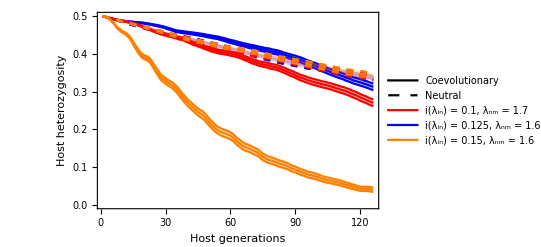

```mathematica
g=Show[ListLinePlot[{mean[parsN1],mean[parsN1]+(2SD[parsN1])/Sqrt[2000],mean[parsN1]-(2SD[parsN1])/Sqrt[2000]},PlotStyle->Directive[Blue,Dashed],Filling->{2->{{3},{Directive[Blue,Opacity[0.2]]}}}],ListLinePlot[{mean[pars1],mean[pars1]+(2SD[pars1])/Sqrt[2000],mean[pars1]-(2SD[pars1])/Sqrt[2000]},PlotStyle->Directive[Blue],Filling->{2->{{3},{Directive[Blue,Opacity[0.2]]}}}],
ListLinePlot[{mean[parsN2],mean[parsN2]+(2SD[parsN2])/Sqrt[2000],mean[parsN2]-(2SD[parsN2])/Sqrt[2000]},PlotStyle->Directive[Red,Dashed],Filling->{2->{{3},{Directive[Red,Opacity[0.2]]}}}],ListLinePlot[{mean[pars2],mean[pars2]+(2SD[pars2])/Sqrt[2000],mean[pars2]-(2SD[pars2])/Sqrt[2000]},PlotStyle->Directive[Red],Filling->{2->{{3},{Directive[Red,Opacity[0.2]]}}}],
ListLinePlot[{mean[parsN3],mean[parsN3]+(2SD[parsN3])/Sqrt[2000],mean[parsN3]-(2SD[parsN3])/Sqrt[2000]},PlotStyle->Directive[Orange,Dashed],Filling->{2->{{3},{Directive[Orange,Opacity[0.2]]}}}],
ListLinePlot[{mean[pars3],mean[pars3]+(2SD[pars3])/Sqrt[2000],mean[pars3]-(2SD[pars3])/Sqrt[2000]},PlotStyle->Directive[Orange],Filling->{2->{{3},{Directive[Orange,Opacity[0.2]]}}}],
PlotRange-> {0,0.5},Frame->True,FrameLabel-> {"Host generations","Host heterozygosity"},Axes-> False,Epilog->Inset[leg,Scaled[{0.25,0.25}]]]
```

```mathematica
Export["/Users/madeline/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/TwoPatch_Discrete_Series.png",g,"PNG",ImageResolution-> 300]
```

/Users/madeline/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/TwoPatch_Discrete_Series.png

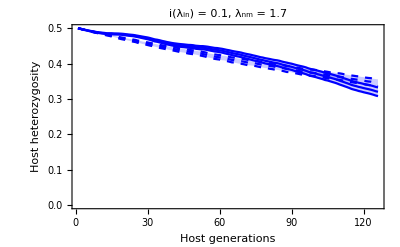

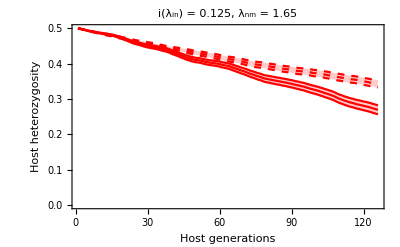

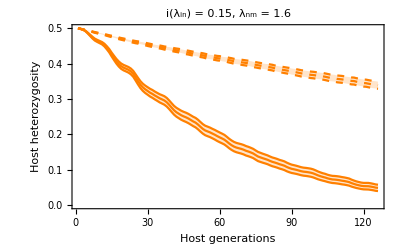

```mathematica
a=Show[ListLinePlot[{mean[parsN1],mean[parsN1]+(2SD[parsN1])/Sqrt[1000],mean[parsN1]-(2SD[parsN1])/Sqrt[1000]},PlotStyle->Directive[Blue,Dashed],Filling->{2->{{3},{Directive[Blue,Opacity[0.2]]}}}],ListLinePlot[{mean[pars1],mean[pars1]+(2SD[pars1])/Sqrt[1000],mean[pars1]-(2SD[pars1])/Sqrt[1000]},PlotStyle->Directive[Blue],Filling->{2->{{3},{Directive[Blue,Opacity[0.2]]}}}],PlotRange-> {0,0.5},Frame->True,PlotLabel-> "i(λ_in) = 0.1, λ_nm = 1.7",FrameLabel-> {"Host generations","Host heterozygosity"},Axes-> False]

b=Show[ListLinePlot[{mean[parsN2],mean[parsN2]+(2SD[parsN2])/Sqrt[1000],mean[parsN2]-(2SD[parsN2])/Sqrt[1000]},PlotStyle->Directive[Red,Dashed],Filling->{2->{{3},{Directive[Red,Opacity[0.2]]}}}],ListLinePlot[{mean[pars2],mean[pars2]+(2SD[pars2])/Sqrt[1000],mean[pars2]-(2SD[pars2])/Sqrt[1000]},PlotStyle->Directive[Red],Filling->{2->{{3},{Directive[Red,Opacity[0.2]]}}}],PlotRange-> {0,0.5},Frame->True,PlotLabel-> "i(λ_in) = 0.125, λ_nm = 1.65",FrameLabel-> {"Host generations","Host heterozygosity"},Axes-> False]
c=Show[ListLinePlot[{mean[parsN3],mean[parsN3]+(2SD[parsN3])/Sqrt[1000],mean[parsN3]-(2SD[parsN3])/Sqrt[1000]},PlotStyle->Directive[Orange,Dashed],Filling->{2->{{3},{Directive[Orange,Opacity[0.2]]}}}],
ListLinePlot[{mean[pars3],mean[pars3]+(2SD[pars3])/Sqrt[1000],mean[pars3]-(2SD[pars3])/Sqrt[1000]},PlotStyle->Directive[Orange],Filling->{2->{{3},{Directive[Orange,Opacity[0.2]]}}}],PlotRange-> {0,0.5},Frame->True,PlotLabel-> "i(λ_in) = 0.15, λ_nm = 1.6",FrameLabel-> {"Host generations","Host heterozygosity"},Axes-> False]
```

/Users/madeline/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/TwoPatch_Discrete_Series_c.png

/Users/madeline/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/TwoPatch_Discrete_Series_b.png

/Users/madeline/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/TwoPatch_Discrete_Series_a.png

/Users/madeline/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/TwoPatch_Discrete_Series.png

/Users/madeline/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/TwoPatch_Discrete_Series.png

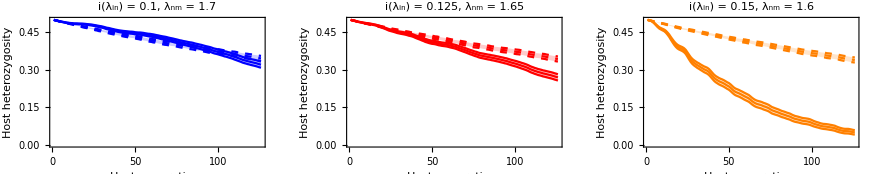

```mathematica
Export["/Users/madeline/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/TwoPatch_Discrete_Series_a.png",a,"PNG",ImageResolution-> 300]
Export["/Users/madeline/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/TwoPatch_Discrete_Series_b.png",b,"PNG",ImageResolution-> 300]
Export["/Users/madeline/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/TwoPatch_Discrete_Series_c.png",c,"PNG",ImageResolution-> 300]
```

```mathematica
Export["~/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/TwoPatch_Discrete_Facet.png",Show[g],ImageResolution->300]
```

~/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/TwoPatch_Discrete_Facet.png

~/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/TwoPatch_Discrete_Facet.png

## Discrete Island-Mainland

```mathematica
Clear[q1,q2,q3,q4,a,b,c,sub]
```

```mathematica
q2=(S √((S-2)V((S-2)V-2)))/((S-2)((S-2)V-2));(*Internal cycling and internal instability*)
q3=(1-V(1-S))/(1-V);(*Matching boundary*)
q4=1/(1-S);(*Non-matching boundary*)
```

```mathematica
sub=Solve[{q2==a, q4==b},{S,V}][[1]]//FullSimplify
```

{S→(-1+b)/b,V→-(2 a^2 b (1+b))/(-(-1+b)^2+a^2 (1+b)^2)}

```mathematica
q2/.sub//FullSimplify
```

(√((a^2 (-1+b^2)^2)/(((-1+b)^2-a^2 (1+b)^2)^2)) ((-1+b)^2-a^2 (1+b)^2))/(-1+b^2)

```mathematica
q4/.sub/.a-> 0.2/.b-> 1.1
```

26.159

### Individual-Based Simulations

```mathematica
alist={0.1,0.1,0.1,0.125,0.125,0.125,0.15,0.15,0.15};
blist={1.6,1.65,1.7,1.6,1.65,1.7,1.6,1.65,1.7};
```

Absolute fitness values

```mathematica
Clear[WH]
WH[1,pVec_]:=pVec[[2]](1-V) +(1-pVec[[2]])S +(1-pVec[[2]])(1-S)(1-V);
WH[2,pVec_]:=(1-pVec[[2]])(1-V)+pVec[[2]]S +pVec[[2]](1-S)(1-V)  ;
WP[1,pVec_]:=pVec[[1]]+(1-pVec[[1]])(1-S);
WP[2,pVec_]:=(1-pVec[[1]])+pVec[[1]](1-S);
```

Relative fitness values

```mathematica
Clear[wH]
wH[pVec_]:=WH[1,pVec]/(pVec[[1]] WH[1,pVec]+(1-pVec[[1]])WH[2,pVec]) ;
wP[pVec_]:=WP[1,pVec]/(pVec[[2]] WP[1,pVec]+(1-pVec[[2]])WP[2,pVec]) ;
```

```mathematica
Clear[Sim]
Sim[pars_,intS_]:=Sim[pars,intS]=Block[{out,g,nH1s,nP1s,nH2s,nP2s,nMH1,nMH2,nMP1,nMP2,nMH11,nMH12,nMH21,nMH22,nMP11,nMP12,nMP21,nMP22,nH1sm,nH2sm,nP1sm,nP2sm,nH11sm,nH21sm,nH12sm,nH22sm,nP11sm,nP12sm,nP21sm,nP22sm,nH1prime,nH2prime,nP1prime,nP2prime},out={{1/2,1/2}}//N;
For[g=1,g≤(tMax/.pars),g++,

(*Selection*)
nH1s=RandomVariate[BinomialDistribution[(κH/.pars),Min[Max[wH[out[[-1]]]out[[-1,1]]/.pars,0],1]]];
nP1s=RandomVariate[BinomialDistribution[(κP/.pars),Min[Max[wP[out[[-1]]]out[[-1,2]]/.pars,0],1]]];

(*Total number of host migrants from populations 1 and 2*)
nMH1=RandomVariate[BinomialDistribution[κH/.pars,mH/.pars]];
nMH2=RandomVariate[BinomialDistribution[κH/.pars,mH/.pars]];

(*Number of type 1 host migrants out of population 1*)
nMH11=RandomVariate[BinomialDistribution[nMH1,nH1s/κH/.pars]];
nMH21=RandomVariate[BinomialDistribution[nMH2,1/2]];

(*Number of type 2 host migrants out of population 1*)
nMH12=nMH1-nMH11;
nMH22=nMH2-nMH21;

(*Number of type 1 and type 2 hosts after migration for populations 1 and 2*)
nH11sm=(nH1s-nMH11+nMH21);
nH12sm=(κH-nH1s)-nMH12+nMH22/.pars;

(*Number of type 1 hosts in next generation*)
nH1prime=RandomVariate[BinomialDistribution[κH/.pars,Min[Max[nH11sm/(nH11sm+nH12sm)//N,0],1]]];

(*Total number of parasite migrants from populations 1 and 2*)
nMP1=RandomVariate[BinomialDistribution[κP/.pars,mP/.pars]];
nMP2=RandomVariate[BinomialDistribution[κP/.pars,mP/.pars]];

(*Number of type 1 parasite migrants out of populations 1 and 2*)
nMP11=RandomVariate[BinomialDistribution[nMP1,nP1s/κP/.pars]];
nMP21=RandomVariate[BinomialDistribution[nMP2,1/2]];

(*Number of type 2 parasite migrants out of populations 1 and 2*)
nMP12=nMP1-nMP11;
nMP22=nMP2-nMP21;

(*Number of type 1 and type 2 hosts after migration for populations 1 and 2*)
nP11sm=(nP1s-nMP11+nMP21);
nP12sm=(κP-nP1s)-nMP12+nMP22/.pars;

(*Number of type 1 hosts in next generation*)
nP1prime=RandomVariate[BinomialDistribution[κP/.pars,Min[Max[nP11sm/(nP11sm+nP12sm)//N,0],1]]];

AppendTo[out,{nH1prime/κH,nP1prime/κP}/.pars//N]
];
out
]
```

```mathematica
Clear[parIter]
parIter[p_,intS_]:=parIter[p,intS]=Block[{SChoice,VChoice,aChoice,bChoice,parsN,parsC,HC,HN},

aChoice=alist[[p]];
bChoice=blist[[p]];
SChoice=Table[(sub/.a->aChoice/.b->bChoice)[[i,2]],{i,1,2}][[1]];
VChoice=Table[(sub/.a->aChoice/.b->bChoice)[[i,2]],{i,1,2}][[2]];

parsN={S-> 0,V->VChoice,mH->0.01,mP->0.01,κH-> 300,κP->300,tMax->125};
parsC={S-> SChoice,V->VChoice,mH->0.01,mP->0.01,κH->300,κP->300,tMax->125};

For[r=1,r≤intS,r++,
Sim[parsC,r];
Sim[parsN,r];
];

HN=Mean[Table[2 (1/2(Sim[parsN,j][[tMax/.parsN,1]]+Sim[parsN,j][[tMax/.parsN,2]]))(1-1/2(Sim[parsN,j][[tMax/.parsN,1]]+Sim[parsN,j][[tMax/.parsN,2]])),{j,1,intS}]];
HC=Mean[Table[2 (1/2(Sim[parsC,j][[tMax/.parsC,1]]+Sim[parsC,j][[tMax/.parsC,2]]))(1-1/2(Sim[parsC,j][[tMax/.parsC,1]]+Sim[parsC,j][[tMax/.parsC,2]])),{j,1,intS}]];

HC-HN

];
```

```mathematica
Table[parIter[i,2000],{i,1,9}]
```

{-0.0279453,-0.024746,-0.0324977,-0.0381983,-0.0315037,-0.0249818,-0.0577349,-0.0603313,-0.0551047}

```mathematica
parIter[9,2000]
```

-0.0125608

```mathematica
p=7;
aChoice=alist[[p]];
bChoice=blist[[p]];
SChoice=Table[(sub/.a->aChoice/.b->bChoice)[[i,2]],{i,1,2}][[1]];
VChoice=Table[(sub/.a->aChoice/.b->bChoice)[[i,2]],{i,1,2}][[2]];

parsN={S-> 0,V->VChoice,mH-> 0.05,mP-> 0.05,κH->150,κP->150,tMax->125}
parsC={S-> SChoice,V->VChoice,mH-> 0.05,mP-> 0.05,κH->150,κP->150,tMax->125}
```

{S→0,V→0.900433,mH→0.05,mP→0.05,κH→150,κP→150,tMax→125}

{S→0.375,V→0.900433,mH→0.05,mP→0.05,κH→150,κP→150,tMax→125}

```mathematica
parsN1={S->0,V->0.2200911052505395,mH->0.05,mP->0.05,κH->150,κP->150,tMax->125};
parsN2={S->0,V->0.4368677407268642,mH->0.05,mP->0.05,κH->150,κP->150,tMax->125};
parsN3={S->0,V->0.9004329004329,mH->0.05,mP->0.05,κH->150,κP->150,tMax->125};
pars1={S->0.4117647058823529,V->0.2200911052505395,mH->0.05,mP->0.05,κH->150,κP->150,tMax->125};
pars2={S->0.3939393939393939,V->0.4368677407268642,mH->0.05,mP->0.05,κH->150,κP->150,tMax->125};
pars3={S->0.37500000000000006,V->0.9004329004329,mH->0.05,mP->0.05,κH->150,κP->150,tMax->125};
```

```mathematica
mean[pars_]:=mean[pars]=Mean[Table[2 ((Sim[pars,j][[;;,1]]+Sim[pars,j][[;;,2]])/2)(1-(Sim[pars,j][[;;,1]]+Sim[pars,j][[;;,2]])/2),{j,1,2000}]]
```

```mathematica
mean[parsN1]//Dimensions
```

{126}

```mathematica
Clear[SD]
SD[pars_]:=SD[pars]=Mean[Table[(2 ((Sim[pars,j][[;;,1]]+Sim[pars,j][[;;,2]])/2)(1-(Sim[pars,j][[;;,1]]+Sim[pars,j][[;;,2]])/2)-mean[pars])^2,{j,1,1000}]]//Sqrt;
```

```mathematica
SD[parsN1]
```

{0.,0.00473118,0.00855622,0.0123217,0.0156021,0.0187244,0.0208128,0.0221464,0.024457,0.0271276,0.0289869,0.0294279,0.0314628,0.0330973,0.0346513,0.0347219,0.0334417,0.0340315,0.0333755,0.0332575,0.0336732,0.0362626,0.0362582,0.0356295,0.0358617,0.0368994,0.0386663,0.0395305,0.0395624,0.0402515,0.0393167,0.0369571,0.0374179,0.0370199,0.0355172,0.0350001,0.0350655,0.0359084,0.0357627,0.0356823,0.0371036,0.0362626,0.036455,0.0375547,0.0379558,0.0391051,0.0391338,0.0392505,0.0403905,0.0413878,0.0405237,0.0400931,0.0412264,0.0397764,0.0397223,0.0395741,0.038658,0.037315,0.0369972,0.0373719,0.038625,0.0379872,0.039154,0.0387744,0.0397197,0.039392,0.0392084,0.0394138,0.0404413,0.0398421,0.0388169,0.0400615,0.0392045,0.038703,0.0392405,0.0404667,0.0406785,0.0399354,0.0402111,0.0394652,0.0388685,0.0389652,0.0382625,0.0398532,0.0408467,0.0428022,0.042938,0.0426631,0.0420431,0.0423907,0.0415756,0.0414563,0.0411917,0.0408808,0.0416858,0.0406882,0.0422924,0.0404825,0.0400735,0.0409295,0.0403978,0.0402488,0.0406214,0.0391778,0.0386632,0.0398602,0.0405049,0.0399294,0.0395508,0.0400193,0.0418014,0.0428763,0.0422407,0.0409542,0.0401982,0.0388305,0.0403532,0.0400534,0.0404743,0.040812,0.0421186,0.0423484,0.0409129,0.0412506,0.0423425,0.0408974}

```mathematica
leg=LineLegend[{Directive[Black],
Directive[Black,Dashed],
Directive[Red],
Directive[Blue],
Directive[Orange]},
{"Coevolutionary","Neutral",
 "i(λ_in) = 0.1, λ_nm = 1.7",
 "i(λ_in) = 0.125, λ_nm = 1.65",
 "i(λ_in) = 0.15, λ_nm = 1.6"}];
```

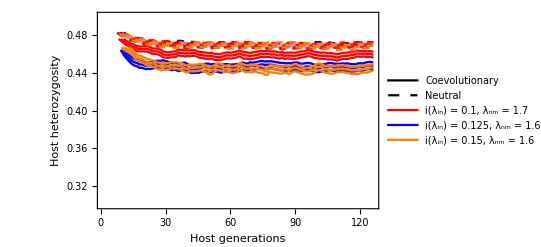

```mathematica
g=Show[ListLinePlot[{mean[parsN1],mean[parsN1]+(2SD[parsN1])/Sqrt[1000],mean[parsN1]-(2SD[parsN1])/Sqrt[1000]},PlotStyle->Directive[Blue,Dashed],Filling->{2->{{3},{Directive[Blue,Opacity[0.2]]}}}],ListLinePlot[{mean[pars1],mean[pars1]+(2SD[pars1])/Sqrt[1000],mean[pars1]-(2SD[pars1])/Sqrt[1000]},PlotStyle->Directive[Blue],Filling->{2->{{3},{Directive[Blue,Opacity[0.2]]}}}],
ListLinePlot[{mean[parsN2],mean[parsN2]+(2SD[parsN2])/Sqrt[1000],mean[parsN2]-(2SD[parsN2])/Sqrt[1000]},PlotStyle->Directive[Red,Dashed],Filling->{2->{{3},{Directive[Red,Opacity[0.2]]}}}],ListLinePlot[{mean[pars2],mean[pars2]+(2SD[pars2])/Sqrt[1000],mean[pars2]-(2SD[pars2])/Sqrt[1000]},PlotStyle->Directive[Red],Filling->{2->{{3},{Directive[Red,Opacity[0.2]]}}}],
ListLinePlot[{mean[parsN3],mean[parsN3]+(2SD[parsN3])/Sqrt[1000],mean[parsN3]-(2SD[parsN3])/Sqrt[1000]},PlotStyle->Directive[Orange,Dashed],Filling->{2->{{3},{Directive[Orange,Opacity[0.2]]}}}],
ListLinePlot[{mean[pars3],mean[pars3]+(2SD[pars3])/Sqrt[1000],mean[pars3]-(2SD[pars3])/Sqrt[1000]},PlotStyle->Directive[Orange],Filling->{2->{{3},{Directive[Orange,Opacity[0.2]]}}}],
PlotRange-> {0.3,0.5},Frame->True,FrameLabel-> {"Host generations","Host heterozygosity"},Axes-> False,Epilog->Inset[leg,Scaled[{0.3,0.3}]]]
```

```mathematica
Export["/Users/madeline/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/IslandMainland_Discrete_Series.png",g,"PNG",ImageResolution-> 300]
```

/Users/madeline/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/IslandMainland_Discrete_Series.png

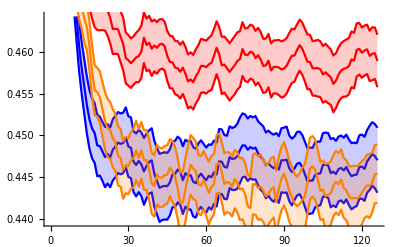

```mathematica
Show[ListLinePlot[{mean[pars1],mean[pars1]+(2SD[pars1])/Sqrt[1000],mean[pars1]-(2SD[pars1])/Sqrt[1000]},PlotStyle->Directive[Blue],Filling->{2->{{3},{Directive[Blue,Opacity[0.2]]}}}],
ListLinePlot[{mean[pars2],mean[pars2]+(2SD[pars2])/Sqrt[1000],mean[pars2]-(2SD[pars2])/Sqrt[1000]},PlotStyle->Directive[Red],Filling->{2->{{3},{Directive[Red,Opacity[0.2]]}}}],
ListLinePlot[{mean[pars3],mean[pars3]+(2SD[pars3])/Sqrt[1000],mean[pars3]-(2SD[pars3])/Sqrt[1000]},PlotStyle->Directive[Orange],Filling->{2->{{3},{Directive[Orange,Opacity[0.2]]}}}]]
```